## Computing for Mathematical Physics 2022/23

# Homework 5

# Mark for homework 5: /32 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Give your answers in the code cells marked (* Enter your solution here *)

Double click the vertical braces on the RHS of each of the question headings to open and view them.

1. Plotting multiple functions on the same graph, labeled, and legended.  [14 marks]

a) Define the wavefunction ψ[n_,x_] in your code according to  
	ψ_n(x) = 1/(√(2^n n!))1/π^(1/4)e^(-1/2 x^2)H_n(x) ,
wherein H_n(x) are the Hermite polynomials, implemented in Mathematica as HermiteH[n,x].

b) Plot ψ_n(x) for n=1,2,3, over the range -5 ≤ x ≤ 5.

• Fix the y-axis range to -0.7 ≤ y ≤ 0.7.
• Use a different colour for each of the three lines plotted.
• Label the axes.
• Include a title “Wavefunctions ψ_n(x)” 
• Include a legend indicating clearly what each line represents.
• Place the legend in the top right of the graph.
• Use LabelStyle to set the Times font family, in Black, with font size 18, for all textual elements.
• Use grid lines.

[14 marks]

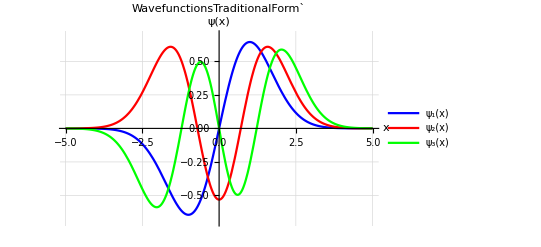

```mathematica
(* Enter code in a new cell immediately below this one. *)
ψ[n_,x_] := 1/(√(2^n n!)) 1/π^(1/4)ⅇ^(-1/2 x^2)*HermiteH[n,x]
Plot[{ψ[1,x],ψ[2,x],ψ[3,x]}, {x,-5,5}, PlotRange->{All,{-0.7,0.7}}, AxesLabel->{x,ψ[x]}, PlotStyle->{Blue,Red,Green},PlotLabel->"WavefunctionsTraditionalForm`", PlotLegends->Placed[LineLegend[{Blue, Red, Green}, {"ψ_1(x)","ψ_2(x)","ψ_3(x)"}],{0.905,0.82}], LabelStyle->{FontFamily->"Times", FontSize->18, FontColor->Black}, GridLines->Automatic]
```

2. Primitive graphics animation. [9 marks]

Point[{x,y}] is a Graphics primitive which represents a point at the position (x,y).
PointSize[...] is a function which sets the size of the point.

Write a piece of code which will represent, as an animation, the motion of a ball oscillating in a harmonic potential well, according to the following steps.

a) Plot y=x^2 over the range -2≤x≤2, with the y axis range limited to -0.2 ≤ y ≤ 4.2, to represent the potential well. Give the plot a frame and gridlines. Call this plot potentialWell.

b) Write a function ballPosition[t_], returning the coordinates, {x,y}, of the the ball at time t, as it oscillates in the potential well. The x coordinate evolves in time according to x = 2 cos(2t), with the corresponding  y coordinate given by the shape of the well in which the ball oscillates.

c) Use Show, inside Animate, to combine the potentialWell plot together with a Graphics object made from a Point, whose position argument is given by ballPosition[t]. Consider which range of values for t will give you a complete cycle in your animation, and select an appropriate time-step.

[Hint: you may need to check Evaluation→Dynamic Updating Enabled is selected in the drop-down menus.]
[9 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
potentialWell = Plot[y=x^2, {x,-2,2}, PlotRange->{All,{-0.2,4.2}}];
ballPosition[t_]:= {2Cos[2t], 4 Cos[2 t]^2}
Animate[Show[Graphics[{PointSize[Large],Red,Point[ballPosition[t]]}],potentialWell,GridLines->Automatic, Frame->True], {t,-2π,2π}]
```

3. Approximate root-finding using Plot. [5 marks]

Use Plot to determine the value of x, between 0 and 10, to 3 significant figures, which solves the equation Log[1/x] == Tanh[x] as follows. Make a Plot showing both Log[1/x] and Tanh[x], and then manually refine the x range (as given in the second argument of Plot), repeatedly, so as to zoom in on the point where the two lines intersect.

You need only display the final plot in the series of plots leading to your final answer. Your answer should be written in a text cell to 3 significant figures.
[5 marks]

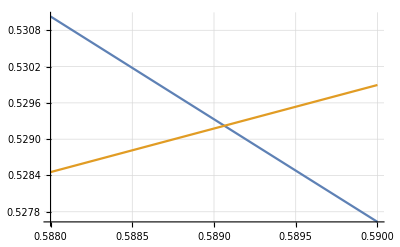

```mathematica
(* Enter code in a new cell immediately below this one. *)
Plot[{Log[1/x],Tanh[x]},{x,0,10}];
Plot[{Log[1/x],Tanh[x]},{x,0,1}];
Plot[{Log[1/x],Tanh[x]},{x,0.5,0.7}];
Plot[{Log[1/x],Tanh[x]},{x,0.58,0.6}];
Plot[{Log[1/x],Tanh[x]},{x,0.588,0.590}, GridLines->Automatic]
```

Root is roughly equal to x = 0.589 (3 s.f)

4. Primitive graphics animation revisited. [4 marks]

This question generalises question 2.

Define a potential V[x_] := 34/31-x^2+x^3+x^4.

a) Plot V[x] over the range -2.5≤x≤2.5, limiting the y-axis range shown to 0≤y≤6.
     Give the plot a frame and gridlines.
     Call this plot q4Well.

b) The equation of motion for a particle moving along the x-axis under the influence of this potential is given by 
       d^2/(d t^2)x[ t ] = -d/(d x)V[ x[ t ] ] 
     where x[t]  is the particle’s position at time t.
     Use NDSolve to solve the equation of motion for  x[t] subject to the boundary conditions 
           x[0] = -2
    x’[0] = 0
     for t in the range 0<t<20.

c) Write a function particle[t_], returning {x[t], V[x[t]]}, with x[t] given by the solution to part b) .

d) Use Show, inside Animate, to combine the q4Well plot together with a Graphics object made from a Point, whose position argument is given by particle[t]. Adjust the animation rate until it is smooth using the AnimationRate option.

[Hint: depending on your approach, it may help to define  particle[t_] with Set, i.e. =, rather than SetDelayed, i.e. :=.]

[4 marks : only fully functioning, correct, solutions for this question are eligible for marks.]

```mathematica
(* Enter code in a new cell immediately below this one. *)
V[x_]:= 34/31-x^2+x^3+x^4
q4well=Plot[V[x], {x,-2.5,2.5}, PlotRange->{All,{0,6}}];
sol=NDSolve[{D[x[t],{t,2}]+ D[V[x[t]],x[t]]==0, x[0]==-2, x'[0]==0},x[t],{t,0,20}]
particle[t_]=Flatten[{Evaluate[x[t]/.sol], Evaluate[V[x[t]]/.sol]}]
Animate[Show[Graphics[{PointSize[Large],Red,Point[particle[t]]}],q4well,GridLines->Automatic, Frame->True],{t,0,20}, AnimationRate->.5]
```

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t],34/31-(InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^3+(InterpolatingFunction[…][t])^4}

Total marks available: 32

Solutions are due by 1200 noon on Thursday February 23rd here:  allow time for uploading on moodle.

A 10% mark deduction will be made (3 marks) if the template isn’t used.

Name your solution notebook file in the format WK5_HMWK_<Initials>_<Family Name>.nb, e.g. WK5_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process with a fresh kernel will produce the output you intend it to, before you upload your work.

K. Hamilton
J. Bhamrah, J. Underwood, A. Harker 
Last revision 13:33 07 Feb 2023